# Math 223: Homework 11

<Hardeep Bassi>

<05/03/2023>

## Problem 1

For the van der Pol oscillator, , apply the method of multiple scales and show that it has a stable limit cycle that is nearly circular with radius .

Using the method of time averaging, we see that we can take . This means we compute the following integrals:

```mathematica
Integrate[-(Sin[θ]^2*Cos[θ]^2)/(2π),{θ,0,2π}]
```

-1/8

```mathematica
Integrate[Sin[θ]^2/(2π),{θ,0,2π}]
```

1/2

This yields that the first average equation is given by . To solve for , we take:

```mathematica
DSolve[r'[τ]+r[τ]^3/8-r[τ]/2==0,r[τ],τ]
```

{{r[τ]→-(2 ⅇ^(τ/2))/(√(ⅇ^τ+ⅇ^(8 C[1])))},{r[τ]→(2 ⅇ^(τ/2))/(√(ⅇ^τ+ⅇ^(8 C[1])))}}

Since we are discussing the radius, we take the positive solution. Taking the limit of this solution yields:

```mathematica
Limit[(2 ⅇ^(τ/2))/(√(ⅇ^τ+ⅇ^(8 C[1]))),τ->∞]
```

2

This means that the amplitude of the oscillator has a stable limit cycle with a radius of  .

## Problem 2

Use the method of multiple scales to study  Describe the long time behavior of the solution based on your results.

Using the method of time averaging yields . This means we compute the following integral:

```mathematica
Integrate[-(Sin[θ]^2*Cos[θ]^2)/(2π),{θ,0,2π}]
```

-1/8

This means that the first averaged equation is given by . To solve for , we take:

```mathematica
DSolve[r'[τ]+r[τ]^3/8==0,r[τ],τ]
```

{{r[τ]→-2/(√(τ-8 C[1]))},{r[τ]→2/(√(τ-8 C[1]))}}

Now we compute the second averaged equation given by:

```mathematica
Integrate[-(Sin[θ]*Cos[θ]^3)/(2π),{θ,0,2π}]
```

0

This means that the second averaged equation is given by . Taking both of theses together, we can solve for . First we see that:

We also see that:
.

From here, we see that to satisfy the conditions of , we have:
 and . In order to have a solution for , we can satisfy the second condition by taking . This means the leading behavior is given by:
.
To validate, we see:

```mathematica
truesol = NDSolveValue[{y''[t]+y[t]+0.001*y[t]^2*y'[t]==0,y[0]==1,y'[0]==0},y,{t,0,40}]
```

InterpolatingFunction[…]

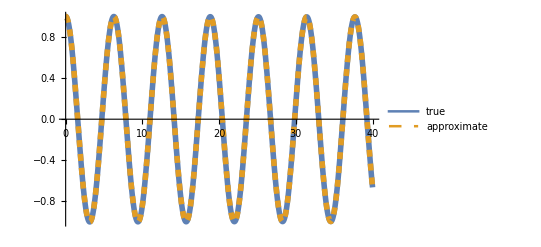

```mathematica
Plot[{truesol[t],2/(√(0.001*t+4))Cos[t]},{t,0,40},PlotStyle-> {Directive[Solid,Thickness[0.01]], Directive[Dashed,Thickness[0.01]]}, PlotLegends->{"true","approximate"},PlotRange->All]
```

The limiting behavior then shows that our approximation does in fact decay to 0:

```mathematica
Limit[(2 Cos[t])/(√(4+t* 0.001)),t->∞]
```

0.